# S-H Phase Plane

```mathematica
ClearAll["Global`*"]
```

## Setup

```mathematica
red=ResourceFunction["HexToColor"]["#FF1F5b"];
green=ResourceFunction["HexToColor"]["#00CD6C"];
blue = ResourceFunction["HexToColor"]["#009ADE"];
purple=ResourceFunction["HexToColor"]["#AF58BA"];
yellow=ResourceFunction["HexToColor"]["#FFC61E"];
orange=ResourceFunction["HexToColor"]["F28522"];
fipar={a->0.07243165880437435,w->0.0026142991079086157,p->27.700459925037663,yn->0.060192963245436854,ds->0.7709975010970849,dh->0.12619563820188512,rc->0.009992087726261166,rn->0.014645292219590888};
parsFixed={nnh->0.18,nns->0.13};
```

## Phase Plane

Here we plotted the rate of change of the symbiont and host for any given S or H.

```mathematica
(*function to calculated rate of change catagory (4 combinations) given an S and H*)
lim2[x_,y_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f,ic,dhdt,dsdt},
ic={h0->y,s0->x};
f=s0(a h0)/(s0+a w h0);(*equation 13*)
jsc=p s0; (*equation 6*)
jsn=yn nnh f; (*equation 5*)
jhc= p s0-Min[jsc,nns^-1 jsn]+rc h0^(2/3);(*equations 10 and 11*)
jhn=rn  h0^(2/3);(*equation 9*)
jsg=Min[jsc,nns^-1 jsn]; (*equation 3*)
jst=ds s0; (*equation 4*)
jhg=Min[jhc,nnh^-1 jhn];(*equation 7*)
jht=dh h0 + f;(*equation 8*)
dhdt=jhg-jht;
dsdt=jsg-jst;
If[(dhdt>0∧dsdt>0)/.fipar/.ic/.parsFixed,1(*Print["SgHg"]*),
If[(dhdt>0∧dsdt<0)/.fipar/.ic/.parsFixed,2(*Print["SlHg"]*),
If[(dhdt<0∧dsdt>0)/.fipar/.ic/.parsFixed,3(*Print["SgHl"]*),4(*Print["SlHl"]*)]]]]
```

```mathematica
out3=Table[
Table[lim2[s,h],{s,10^-15,.001,.00002}],{h,0,0.1,.002}];(*calculate a large number of S and H combinations*)plotout=ArrayPlot[Reverse[out3],AspectRatio->1,ColorRules->{1->purple,2->yellow,3->green,4->blue},Mesh->True,PlotLegends->SwatchLegend[{"S'>0 and H'>0","S'<0 and H'>0","S'>0 and H'<0","S'<0 and H'<0"},LegendLabel->"Sign of Derivatives"],Frame->True,FrameLabel->{"H (C-mol)","S (C-mol)"},FrameTicks->{Reverse[Table[{51-h/2,0.001h},{h,0,100,10}]],Table[{s/2+1,s 0.00001},{s,0,100,20}]},PlotRange->Full,LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},ImageSize->600];(*plot S and H comination with corrispondint rates of change*)
```

{27.3688,35.9974}

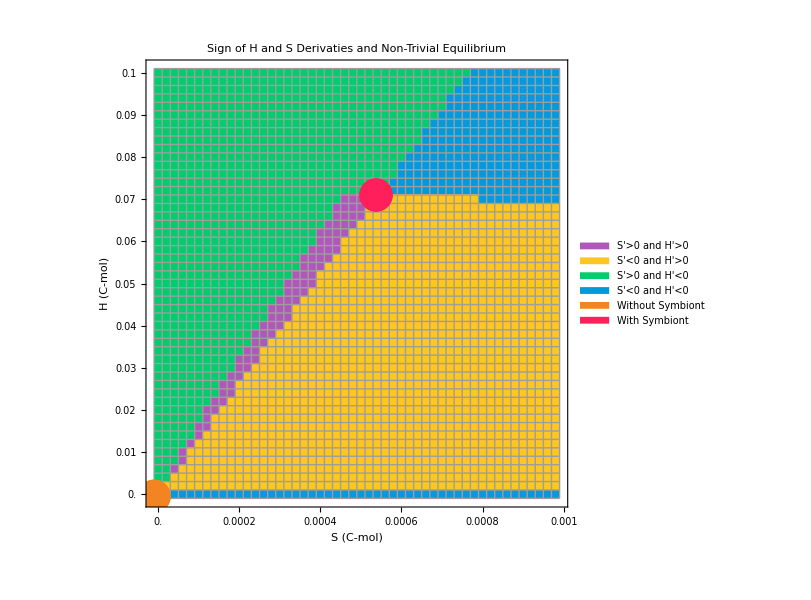

```mathematica
eq1= {0,0.0004964044681961489};(*equilibrium*)
eq1o={0,500 0.0004964044681961489};(*equilibrium adjusted for plot*)
eq2={0.000539286,0.0705831};(*equilibrium*)
eq2o={50750 0.000539286,510 0.0705831}(*equilibrium adjusted for plot*)
plotoutnew=Show[plotout,
ListPlot[{{eq1o},{eq2o}},PlotStyle->{{orange,PointSize[.04]},{red,PointSize[.04]}},PlotLegends->SwatchLegend[{"Without Symbiont","With Symbiont"},LegendLabel->"Non-Trivial Equilibrium",LegendMarkers->"Bubble"],LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15}],PlotLabel->Style["Sign of H and S Derivaties and Non-Trivial Equilibrium",FontSize->25]](*add equalibrium to plot*)
```

Here we see the four possible regimes of growth and turnover for the host and symbiont. There are two non-trivial equilibrium. It is important to note that the “without symbionts” equilibrium is not a trivial equilibrium and is (0,0.0005). The with symbiont equilibrium is significantly larger than the without equilibrium, as the symbiont support the host to reach a higher equilibrium. At the with symbiont equilibrium, the host is approximately 20mm in basal disk diameter which is slightly larger than E. pallida are naturually found to be (Verril, 1864). This is because this mode does not incorporate reproduction. E. pallida reproduce before they reach this size in nature.

## References

Addison Emery Verrill . Revision of the polypi of the eastern coast of the
united states . 1864.